```mathematica
ClearAll[spcd];
spcd[a_,a_]:=spcd[a,a]=CatalanNumber[a];
spcd[a_,b_]:=spcd[a,b]=Sum[CatalanNumber[i]spcd[a-i-1,b-i],{i,0,b}]
```

```mathematica
Table[spc[a,b],{a,0,10},{b,0,a}]//TableForm
```

1 |  |  |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  |  |  | 
1 | 2 | 2 |  |  |  |  |  |  |  | 
1 | 3 | 5 | 5 |  |  |  |  |  |  | 
1 | 4 | 9 | 14 | 14 |  |  |  |  |  | 
1 | 5 | 14 | 28 | 42 | 42 |  |  |  |  | 
1 | 6 | 20 | 48 | 90 | 132 | 132 |  |  |  | 
1 | 7 | 27 | 75 | 165 | 297 | 429 | 429 |  |  | 
1 | 8 | 35 | 110 | 275 | 572 | 1001 | 1430 | 1430 |  | 
1 | 9 | 44 | 154 | 429 | 1001 | 2002 | 3432 | 4862 | 4862 | 
1 | 10 | 54 | 208 | 637 | 1638 | 3640 | 7072 | 11934 | 16796 | 16796

```mathematica
spcdtimings=Table[
ClearAll[spcd];
spcd[a_,a_]:=spcd[a,a]=CatalanNumber[a];
spcd[a_,b_]:=spcd[a,b]=Sum[CatalanNumber[i]spcd[a-i-1,b-i],{i,0,b}];
AbsoluteTiming[spcd[3b,b]],
{b,0,60}];
```

```mathematica
spctimings=Table[
ClearAll[spc];
spc[a_,a_]:=spc[a,a]=CatalanNumber[a];
spc[a_,b_]:=spc[a,b]=Sum[spc[i,i]spc[a-i-1,b-i],{i,0,b}];
AbsoluteTiming[spc[3b,b]],
{b,0,60}];
```

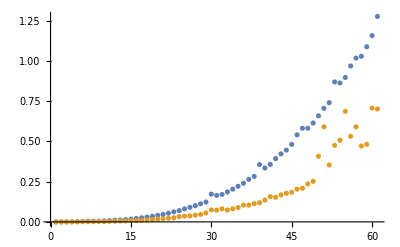

```mathematica
ListPlot[{First/@spcdtimings,First/@spctimings}]
```

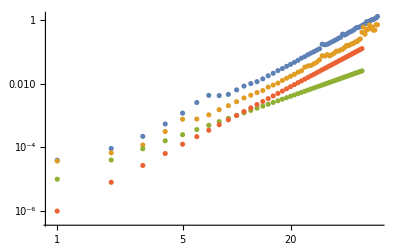

```mathematica
ListLogLogPlot[{First/@spcdtimings,First/@spctimings,Array[#^2/100000&,50],Array[#^3/1000000&,50]}]
```

```mathematica
timings=Table[AbsoluteTiming[CatalanNumber[n]],{n,0,100000}];
```

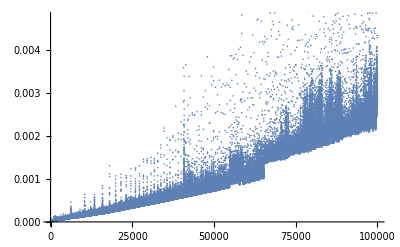

```mathematica
ListPlot[First/@timings]
```

```mathematica
spc[a_,a_]:=spc[a,a]=CatalanNumber[a];
spc[a_,b_]:=spc[a,b]=Sum[spc[i,i]spc[a-i-1,b-i],{i,0,b}];
```